```mathematica
MatrixG = 900
NumberOfMatricesG = 10
```

900

10

```mathematica
(* for Normal or Gaussian distribution we need to know standart deviation and expectation of the distribution witch equal to zero.*)
variance = 1 / MatrixG; 
standartDeviation = Sqrt[variance]; 
d = NormalDistribution[0, standartDeviation]; 

GMatrices = Array[0,0]; 
i = 1; 
For [i = 1, i ≤ NumberOfMatricesG , i ++, SeedRandom[]; 
AppendTo[GMatrices, RandomReal[d, {MatrixG, MatrixG}]]
] 

(*We can compute a singular values for G matrix of G matrices family*)
```

```mathematica
SingularValuesG = Array[0,0]; 
startTime = AbsoluteTime[]; 
For[i = 1, i ≤ NumberOfMatricesG, i++, 
AppendTo[SingularValuesG, SingularValueList[GMatrices[[i]]]]
]
endTime = AbsoluteTime[]- startTime


ConditionNumbers = Array[0,0]; 
For [i = 1, i ≤ NumberOfMatricesG, i++, 
(*In this part of program we compute the condition number (maxSV/minSV) *)
AppendTo[ConditionNumbers, Max[SingularValuesG[[i]]]/Min[SingularValuesG[[i]]]]]; 

(*This is mean of log(condition numbers)*)
Print[ConditionNumbers]
log = Mean[Log[ConditionNumbers]]
```

1.03001

{3444.31,1454.39,10714.5,4777.85,2983.71,17847.,15999.8,210260.,5539.84,235994.}

9.38961

{{1000,1.59},{1500,6.1},{1800,10.36},{3000,47.13},{3500,77.46},{2000,14.17}}

1.79658×10^-9 x^3

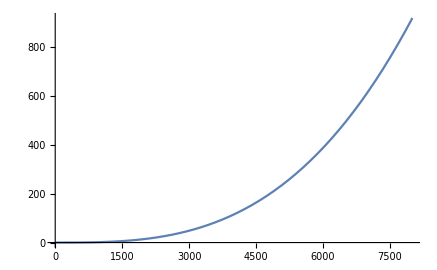

```mathematica
results = {{1000, 1.59}, {1500, 6.10}, {1800, 10.36}, {3000, 47.13}, {3500,77.46 }, {2000, 14.17}}
f = FindFormula[results, x]
T[x_] = f; 

Plot[T[x], {x, 0, 8000}]
```

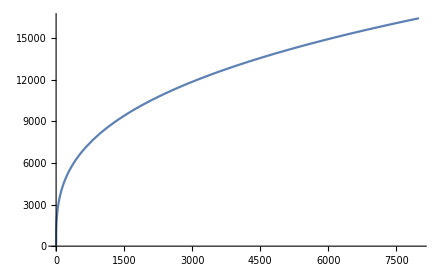

```mathematica
Plot[822.681*x^(1/3),  {x, 0,8000}]
```

```mathematica
logs = {{Log[1000.0],Log[1.59]},{Log[1500.0],Log[6.10]},{Log[1800.0],Log[10.36]},{Log[3000.0],Log[47.13]},{Log[3500.0],Log[77.46]},{Log[2000.0],Log[14.17]}}
f2 = FindFormula[logs, x]
F[x_] = f2;
```

{{6.90776,0.463734},{7.31322,1.80829},{7.49554,2.33795},{8.00637,3.85291},{8.16052,4.34976},{7.6009,2.65113}}

-20.6867+3.06884 x

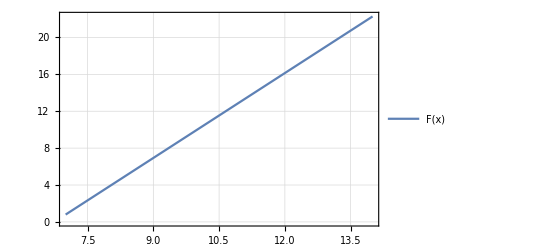

```mathematica
Plot[F[x],{x,7,14},PlotTheme->"Detailed"]
```

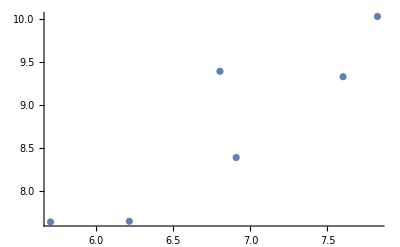

```mathematica
ListPlot[{{Log[1000.0], 8.392542678120403 }, { Log[2000.0], 9.327269137736184}, { Log[2500.0], 10.02384162154796}, { Log[300.0], 7.647776754276637}, { Log[500.0], 7.654594863865375}, { Log[900.0], 9.38961480303997}} ]
```

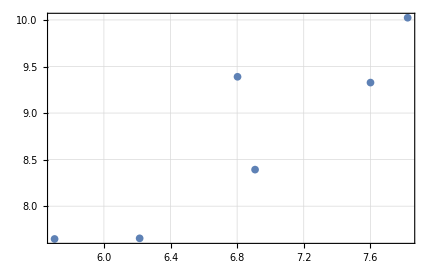

ListPlot::lpn: 8.73927 is not a list of numbers or pairs of numbers.

Plot::nonopt: "Options expected (instead of {y, 0, 500}) beyond position 2 in Plot[Log[x] = Log[y], {x, 0, 500}, {y, 0, 500}]. An option must be a rule or a list of rules."

```mathematica
ListPlot[{{Log[1000.],8.392542678120403},{Log[2000.],9.327269137736184},{Log[2500.],10.02384162154796},{Log[300.],7.647776754276637},{Log[500.],7.654594863865375},{Log[900.],9.38961480303997}},PlotTheme->"Detailed"]
```